## Mathematica 13

## Testing environment on Windows 11

```mathematica
rad[x_]:=x*π/180;
v[x_,y_]:=Exp[x]*Sin[rad[y]];
```

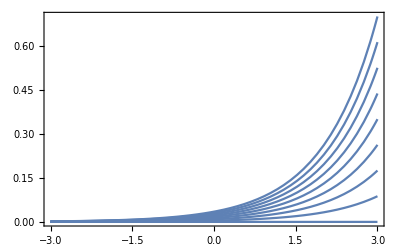

```mathematica
Plot[Table[v[x,y],{y,0,2,0.25}],{x,-3,3},PlotRange->Full,Axes->True,Frame->True]
```